```mathematica
condiciones={a->1};
R20=√(2/a)(1/(2a))(1- r/(2a))Exp[-r/(2a)];
R21=√(1/(6a))*(1/(2 a^2))r Exp[-r/(2a)];
```

```mathematica
R20/.condiciones
R21/.condiciones
```

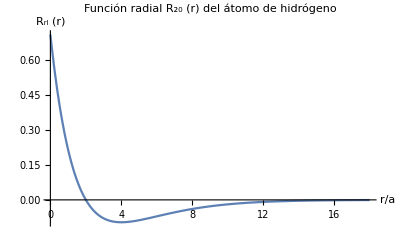

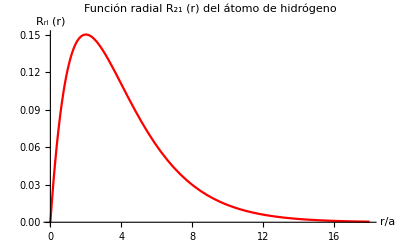

```mathematica
Plot[R20/.condiciones,{r,0,18},PlotRange->All,PlotLabel->Style["Función radial R_20 (r) del átomo de hidrógeno",FontSize->16,Black],AxesLabel->{Style["r/a",14,Black],Style["R_rl (r)",14,Black]}]
Plot[R21/.condiciones,{r,0,18},PlotRange->All,PlotLabel->Style["Función radial R_21 (r) del átomo de hidrógeno",FontSize->16,Black],PlotStyle->Red,AxesLabel->{Style["r/a",14,Black],Style["R_rl (r)",14,Black]}]
```